1. 
Definisikan sebuah fungsi piecewise yang terturunkan di semua titik di real.

Jawab
---------
Sebuah fungsi piecewise yang terturunkan di semua titik yang real apabila pada selalu kontinu, artinya pada titik perubahan fungsi, limit kiri dan limit kanannya sama. Buatlah fungsi yang dapat memenuhi aturan tersebut.

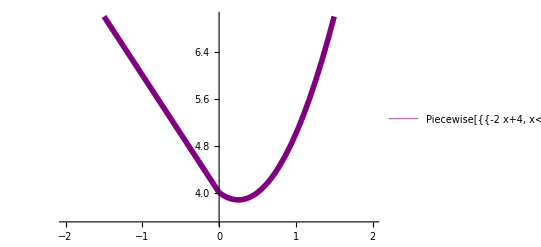

```mathematica
Plot[Piecewise[{{-2x+4,x<0},{2 x^2-x+4,x>0}}],{x,-2,2},PlotRange->{3.5,7},PlotStyle->{Purple,Thickness[0.01]},PlotLegends->"Expressions"]
```

Pada x=0, terdapat kekontinuan dimana kedua fungsi yang diberikan memiliki limit kiri dan limit kanan yang sama.

Maka, contoh fungsi piecewise ini terturunkan pada semua titik di real.

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

2. 
Suatu perusahaan komputer keuntungan penjualannya dituliskan dengan f(x)=x^3-9/2 x^2+23/4 x-15/8. 
Tentukan waktu kapan penjualan tertinggi dan terendahnya, dan berapa keuntungan yang bisa diperoleh pada saat itu?

Jawab
---------

Gunakan konsep turunan untuk mencari titik stasioner

```mathematica
f[x_]:=x^3-9/2 x^2+23/4 x-15/8
```

```mathematica
f'[x]
```

23/4-9 x+3 x^2

```mathematica
Solve[23/4-9 x+3 x^2==0,{x}]
```

{{x→1/6 (9-2 √3)},{x→1/6 (9+2 √3)}}

Kita telah mendapatkan titik stasioner, namun apabila kita memasukkan ini ke dalam fungsi awal tidak akan menyelesaikan masalah, sehingga kita akan ganti √3 dengan kisaran nilainya

```mathematica
N[√3]
```

1.73205

Dari sini, definisikah kembali kedua x

```mathematica
1/6(9-2*1.73205)
```

0.92265

```mathematica
1/6(9+2*1.73205)
```

2.07735

Kita mendapatkan 2 titik stasioner yaitu x=0.92265 dan x=2.07735. Sekarang kita masukkan kembali ke dalam fungsi awal untuk menentukan nilai tertinggi dan nilai terendah.

```mathematica
f[0.92265]
```

0.3849

```mathematica
f[2.07735]
```

-0.3849

Maka x=0.92265 memberikan nilai tertinggi dan x=2.07735 memberikan nilai terendah.

Jadi, perusahaan komputer tersebut memiliki waktu penjualan tertinggi pada x=0.92265 dan waktu penjualan terendah pada x=2.07735 dengan keuntungan yang diperoleh sebesar 0.3849 saat penjualan tertinggi.

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

3. Dengan menggunakan definisi integral Riemann, tentukan nilai limit berikut 
  lim     n^2(1/(n^3+1^3)+1/(n^3+2^3)+1/(n^3+3^3)+...+1/(n^3+n^3))
n→ ∞
Gambarkan juga fungsi yang sesuai untuk bentuk integral Riemann tersebut.

Jawab
---------

Gunakan MRSUM dan tulislah fungsi limit. Kemudian buatlah tabel untuk memperlihatkan distribusi nilai fungsi limit tersebut.

```mathematica
MRSUM[a_,b_,n_]:=Sum[k[a+i*(b-a)/n]*(b-a)/n,{i,0,n-1}]
```

```mathematica
k[x_]:=∑_(n=1)^∞ n^2(1/(n^3+n^3))
TableForm[Table[{n,N[MRSUM[1,∞,n]]},{n,10,50,5}],
TableHeadings->{{},{"n","Riemann Sum"}}]
```

```mathematica
{{, "n", "Riemann Sum"}, {"", 10, ∞}, {"", 15, ∞}, {"", 20, ∞}, {"", 25, ∞}, {"", 30, ∞}, {"", 35, ∞}, {"", 40, ∞}, {"", 45, ∞}, {"", 50, ∞}}
```

Maka dapat dilihat bahwa hasilnya akan selalu ∞, maka Limit dari  n^2(1/(n^3+1^3)+1/(n^3+2^3)+1/(n^3+3^3)+...+1/(n^3+n^3)) adalah ∞

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------
-----------------------------------------------------------------------------------------------------------------------------------------------------------------------

4. Cari luas daerah di bawah f(x)=1-x^2/π dan di atas g(x)=cos x

Jawab
---------
Pertama, definisikan f(x) dan g(x)

```mathematica
f[x_]:=1-x^2/π
g[x_]:=Cos [x]
```

Kemudian, untuk menentukan luas daerahnya, buatlah grafik keduanya menggunakan plot

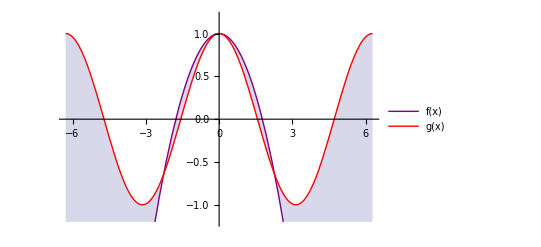

```mathematica
Plot[{f[x],g[x]},{x,-2π,2π},
PlotStyle->{Purple,Red},PlotRange-> {-1.2,1.2},Filling->{1->{2}},PlotLegends->"Expressions"]
```

Dapat dilihat dari gambar bahwa f(x) memiliki fungsi di atas g(x) dan keduanya berpotongan pada beberapa titik. 
Namun perhatikan bahwa soal meminta luas daerah di bawah f(x) dan di atas g(x), sehingga luas sebelum titik potong di kiri dan setelah di kanan tidak diperhitungkan.
Sekarang kita akan mencari titik potong yang akan digunakan, gunakan Solve.

```mathematica
N[Solve[f[x]==g[x],x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Tampaknya sistem tidak dapat menyelesaikan ini sehingga kita dapat menggunakan cara lain yaitu mengulang plotting diatas hingga menemukan titik potong tersebut.

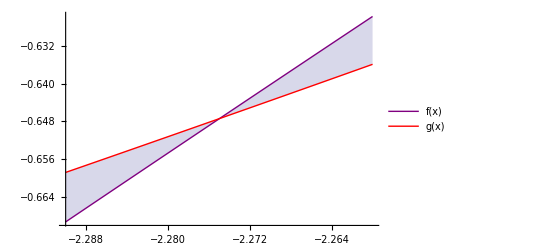

```mathematica
Plot[{f[x],g[x]},{x,-2.29,-2.26},
PlotStyle->{Purple,Red},Filling->{1->{2}},PlotLegends->"Expressions"]
```

Maka kita dapatkan bahwa titik potong di sebelah kiri adalah x=-2.275, lakukan hal yang sama pada sebelah kanan, maka akan didapatkan x=2.275. Selanjutnya kita akan menghitung luasnya.
Perhatikan bahwa f(x) berada di atas g(x), maka dalam menghitung luasnya, f(x) ditulis terlebih dahulu.

```mathematica
Luas=N[Integrate[f[x]-g[x],{x,-2.275,2.275}]]
```

0.527109

Sehingga kita dapatkan luas di bawah f(x) dan di atas g(x) adalah 0.527109